# Q7

0

5

0.5

10.

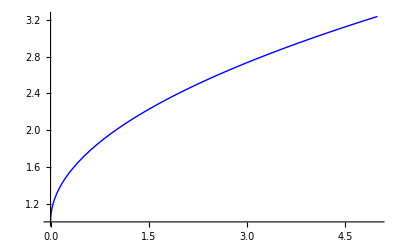

a | b | mid=0.5(a+b) | △xf[a] | △xf[b] | △xf[mid]
0. | 0.5 | 0.25 | 0.5 | 0.853553 | 0.75
0.5 | 1. | 0.75 | 0.853553 | 1. | 0.933013
1. | 1.5 | 1.25 | 1. | 1.11237 | 1.05902
1.5 | 2. | 1.75 | 1.11237 | 1.20711 | 1.16144
2. | 2.5 | 2.25 | 1.20711 | 1.29057 | 1.25
2.5 | 3. | 2.75 | 1.29057 | 1.36603 | 1.32916
3. | 3.5 | 3.25 | 1.36603 | 1.43541 | 1.40139
3.5 | 4. | 3.75 | 1.43541 | 1.5 | 1.46825
4. | 4.5 | 4.25 | 1.5 | 1.56066 | 1.53078
4.5 | 5. | 4.75 | 1.56066 | 1.61803 | 1.58972
Riemann Sum |  |  | 11.8257 | 12.9437 | 12.4728

12.4536

```mathematica
f[x_]:=Sqrt[x]+1
(*i*)
a=0
b=5
h=0.5
(*ii*)
n=(b-a)/h
(*iii*)
Plot[f[x],{x,0,5},PlotStyle->{Blue,Thick}]
(*iv*)
x[i_]=a+(i-1)h;
head = {"a","b","mid=0.5(a+b)","△xf[a]","△xf[b]","△xf[mid]"};
body = Table[{x[i],x[i+1],mid=0.5(x[i]+x[i+1]),h*f[x[i]],h*f[x[i+1]],h*f[mid]},{i,1,n}];
foot={"Riemann Sum",SpanFromLeft,SpanFromLeft,Sum[h*f[x[i]],{i,1,n}],
Sum[h*f[x[i+1]],{i,1,n}],
Sum[h*f[0.5(x[i]+x[i+1])],{i,1,n}]
};
Style[
Grid[
Prepend[
Append[
body,foot
],
head
],
Frame->All,
Background->{None,{LightGreen,{},LightBlue}}
],
Bold
]
(*v&&vi*)
Integrate[f[x],{x,0,5}]//N
```